```mathematica
SetDirectory[NotebookDirectory[]];
Get["calcpi.m"]
```

```mathematica
n = Input["Število naključnih točk n:"]; (*v okno, ki se odpre je potrebno vpisati zgolj število naključno generiranih točk, npr. 1000*)
t0 = tocke[n];
{znotraj,zunaj}=preveri[t0];
```

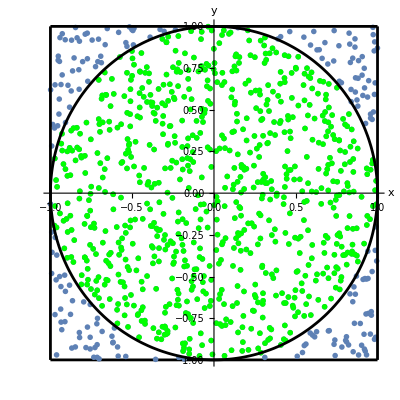

```mathematica
a=ListPlot[t0,PlotStyle->PointSize[0.01],AxesLabel->{"x","y"},AspectRatio->1];
b=ListPlot[znotraj,PlotStyle->{PointSize[0.01],Green},AspectRatio->1];
c=ParametricPlot[{Sin[x],Cos[x]},{x,0,2Pi},PlotStyle->Black,AspectRatio->1];
d=ParametricPlot[{x,1},{x,-1,1},PlotStyle->Black];
e=ParametricPlot[{x,-1},{x,-1,1},PlotStyle->Black];
f=ParametricPlot[{1,x},{x,-1,1},PlotStyle->Black];
g=ParametricPlot[{-1,x},{x,-1,1},PlotStyle->Black];
Show[a,b,c,d,e,f,g,AspectRatio->1]
```

```mathematica
{priblizekPi,napaka}=izracunPi[{znotraj,zunaj}];

Print["Približek Pi pri računanju s ",n," točkami je ",priblizekPi,".\n","Ta od prave vrednosti π odstopa za ",napaka];
```

Približek Pi pri računanju s 1000 točkami je 3.2.
Ta od prave vrednosti π odstopa za 0.0584073

```mathematica
(* izračunal približek π za od 100 do 4000 točk *)
{priblizkiPi,napake}=calcPi[];
t = Table[{i 100,priblizkiPi[[i]]},{i,1,Length[priblizkiPi]}];
```

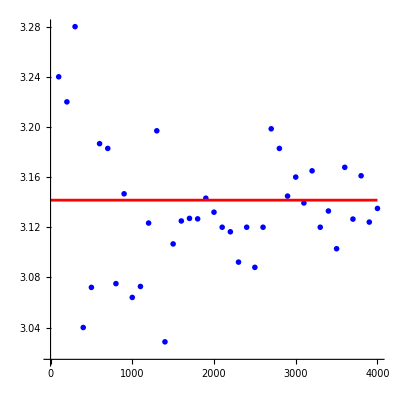

```mathematica
LP1=ListPlot[t,PlotStyle->{PointSize[0.01],Blue},AspectRatio->1];
LP2=ParametricPlot[{x,Pi},{x,0,4000},PlotStyle->Red];
Show[LP1,LP2]
```